## Creating convergence plot

```mathematica
Get[FileNameJoin[{NotebookDirectory[], "GeneticAlgorithmPackage.wl"}]]
```

```mathematica
ClearAll[f2, c2, init2];
init2 = {1,1};
f2[x_] := Min[(1/Abs[3-#])&/@x];
c2[x_] := True;

result = GeneticAlgorithm[init2, f2, {c2}];
result = Transpose[result];
```

```mathematica
resultPlot = Map[
	With[
		{element = #},
		Map[
			With[
				{elementTime = #},
				f2[elementTime]
			]&,
			element
		]
	]&
	,
	result
];
```

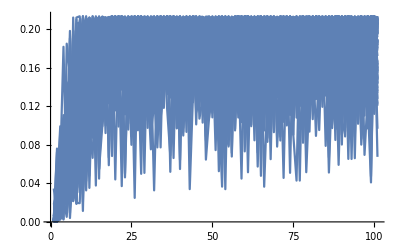

```mathematica
Show[ListLinePlot[#]& /@ resultPlot]
```

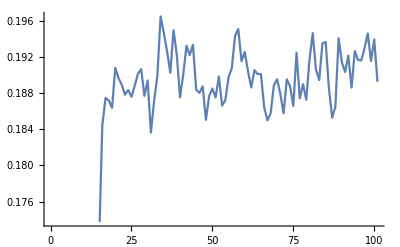

```mathematica
ListLinePlot[Mean[resultPlot]]
```

## Moving dots

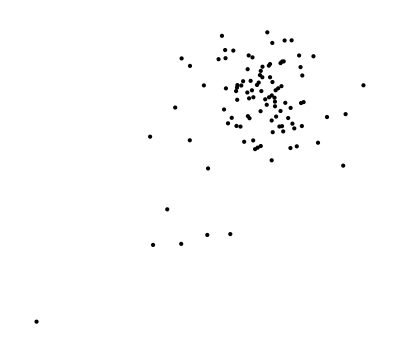

```mathematica
ClearAll[i];
Graphics[Point[#& /@ First[result]]]
Manipulate[
	Show[
		Graphics[
			Point[#[[i]]& /@ result], 
			PlotRange->{{0,4},{0,4}}
		],
		Graphics[{Red, PointSize->Large, Point[{3, 3}]}]
	],
	{i, 1, Length[First[result]]}
]
```

## 3D

```mathematica
Show[Plot3D[Min[1/Abs[3-x],1/Abs[3-y]],{x,0,5},{y,0,5}], Graphics3D[Point[{1, 1, 1}]]]
```

-Graphics3D-

```mathematica
data=RandomVariate[𝒹=MultinormalDistribution[{3,3},{{1,-1/3},{-1/3,2/3}}],10^4];Plot3D[PDF[𝒹,{x,y}],{x,0,6},{y,0,6},ColorFunction->"Rainbow",PlotPoints->35,PlotRange->All]
```

-Graphics3D-

```mathematica
ClearAll[fDistr];
fDistr[x_] := N[PDF[MultinormalDistribution[{3,3},{{1,-1/3},{-1/3,2/3}}], x]];
```

```mathematica
ClearAll[init3];
init3 = {1, 1};
c3[x_] := True;
 
result = GeneticAlgorithm[init3, fDistr, {c3}];
result = Transpose[result];
```

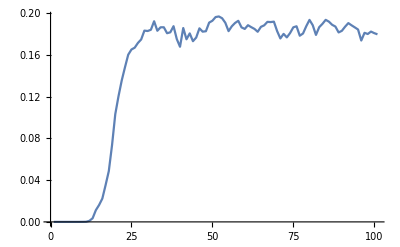

```mathematica
resultPlot = Map[
	With[
		{element = #},
		Map[
			With[
				{elementTime = #},
				fDistr[elementTime]
			]&,
			element
		]
	]&
	,
	result
];
ListLinePlot[Mean[resultPlot]]
```

```mathematica
ClearAll[i];
Manipulate[
	Show[
		Graphics3D[
			Point[{#[[i]][[1]], #[[i]][[2]], fDistr[{#[[i]][[1]], #[[i]][[2]]}]}& /@ result], 
			PlotRange->{{0,4},{0,4}, Automatic}
		],
		Plot3D[fDistr[{x, y}], {x, 0, 4}, {y, 0, 4}, AspectRatio->Automatic, ColorFunction->"Rainbow", Mesh->None, PlotPoints->25],
		BoxRatios->{1, 1, 1}
	],
	{i, 1, Length[First[result]],1}
]
```

```mathematica
ClearAll[i];
Manipulate[
	Show[
		Graphics3D[
			Point[{#[[i]][[1]], #[[i]][[2]], fDistr[{#[[i]][[1]], #[[i]][[2]]}]}& /@ result], 
			PlotRange->{{0,4},{0,4}, Automatic}
		],
		Plot3D[fDistr[{x, y}], {x, 0, 4}, {y, 0, 4}, AspectRatio->Automatic, ColorFunction->"Rainbow", Mesh->None, PlotPoints->25],
		BoxRatios->{1, 1, 1}
	],
	{i, 1, Length[First[result]],1}
]
```

```mathematica
plot3D=Plot3D[fDistr[{x, y}], {x, 0, 4}, {y, 0, 4}, AspectRatio->Automatic, ColorFunction->"Rainbow", Mesh->None, PlotPoints->25,BoxRatios->{1, 1, 1}];
```

```mathematica
graphics=Table[Graphics3D[
			Point[{#[[i]][[1]], #[[i]][[2]], fDistr[{#[[i]][[1]], #[[i]][[2]]}]}& /@ result], 
			PlotRange->{{0,4},{0,4}, Automatic}
		],
		{i, 1, Length[First[result]]}];
```

```mathematica
Manipulate[		
	Show[
		plot3D,
		graphics[[i]]		
	],
	{i, 1, Length[First[result]],1}
]
```